## Oscillator decay time (Prob. 2.3)

```mathematica
Clear["Global`*"];
```

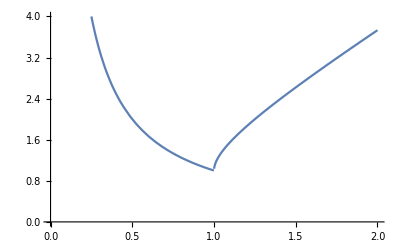

```mathematica
sp=Re[ζ+√(ζ^2-1)];dp=1/sp;
sm=Re[ζ-√(ζ^2-1)];dm=1/sm;
Plot [{dm},{ζ,0.1,2},PlotRange->{0,4}]
```

Thus, the minimum decay time is given by critical damping.  Note the sharp increase (infinite derivative) of the decay time for ζ > 1.  It is then better to err, if need be, on the slightly underdamped side of the optimum.

```mathematica
ysol=DSolveValue[{y''[t]+2ζ y'[t]+y[t]==0,y[0]==1,y'[0]==0},y[t],t]//Simplify
```

(ⅇ^(-t (ζ+√(-1+ζ^2))) ((-1+ⅇ^(2 t √(-1+ζ^2))) ζ+(1+ⅇ^(2 t √(-1+ζ^2))) √(-1+ζ^2)))/(2 √(-1+ζ^2))

```mathematica
ycrit=Limit[ysol,ζ->1]; dycrit=D[ycrit,t]//Simplify;
{ycrit,dycrit}
```

{ⅇ^-t (1+t),-ⅇ^-t t}

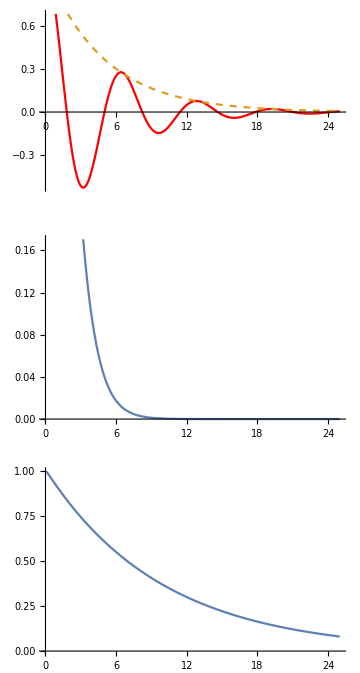

```mathematica
tmax=25;
p1=Plot[{ysol/.ζ->0.2,ⅇ^(-ζ t)/.ζ->0.2},{t,0,tmax},PlotStyle->{Red,Dashed}];
p2=Plot[ycrit,{t,0,tmax}];
p3=Plot[ysol/.ζ->5,{t,0,tmax}];
GraphicsColumn[{p1,p2,p3},ImageSize->Medium]
```